```mathematica
rawData = Import["./selectionParameterBetweenLS.csv"];
header = rawData[[1]]
stages = Drop[header, 2];
deltaEtaData = Drop[rawData, 1];
aaVec = GetColumn[deltaEtaData, 1];
codonVec = GetColumn[deltaEtaData, 2];
aaVals = Union[aaVec]

(*organize data by aa *)
Table[
aaPos = Position[aaVec, aa];
unscaledValues=Drop[
Transpose[
Extract[deltaEtaData, aaPos]
], 1];
(*scale deltaEta values by subtracting off their mean for an AA in a given stage *)
deltaEtaByAA[aa] = Table[
 vals = unscaledValues[[i]];
If[i==1,vals,
vals - Mean[vals]
], {i, Length[unscaledValues]}], {aa, aaVals}]
```

{AA,Codon,Larvae,Dauer,Emb,L3L4,Adult}

{A,C,D,E,F,G,H,I,K,L,N,P,Q,R,S,T,V,Y,Z}

{{{GCA,GCC,GCG,GCT},{1.18332,-1.40284,0.302239,-0.082723},{1.2386,-1.44388,0.26151,-0.0562313},{1.15805,-1.43667,0.363004,-0.0843848},{1.0928,-1.31348,0.282567,-0.0618866},{1.18467,-1.43285,0.301107,-0.052927}},{{TGC,TGT},{-0.767962,0.767962},{-0.754337,0.754337},{-0.743382,0.743382},{-0.680911,0.680911},{-0.733615,0.733615}},{{GAC,GAT},{-0.456264,0.456264},{-0.461114,0.461114},{-0.45918,0.45918},{-0.416421,0.416421},{-0.465748,0.465748}},{{GAA,GAG},{1.0033,-1.0033},{1.01409,-1.01409},{0.985239,-0.985239},{0.933458,-0.933458},{0.992923,-0.992923}},{{TTC,TTT},{-0.637945,0.637945},{-0.691162,0.691162},{-0.653749,0.653749},{-0.600841,0.600841},{-0.668995,0.668995}},{{GGA,GGC,GGG,GGT},{-0.890498,-0.373005,1.04654,0.216965},{-0.94236,-0.427716,1.17987,0.190208},{-0.907635,-0.330282,1.07151,0.166403},{-0.862596,-0.324133,1.0276,0.159128},{-0.904509,-0.333546,1.05586,0.182193}},{{CAC,CAT},{-0.797159,0.797159},{-0.815922,0.815922},{-0.782077,0.782077},{-0.742547,0.742547},{-0.790171,0.790171}},{{ATA,ATC,ATT},{0.974894,-0.941547,-0.0333463},{1.0925,-1.0227,-0.0698021},{0.991363,-0.942231,-0.0491317},{0.932334,-0.85694,-0.0753943},{1.04339,-0.990863,-0.0525239}},{{AAA,AAG},{1.12365,-1.12365},{1.12958,-1.12958},{1.12835,-1.12835},{1.05259,-1.05259},{1.14066,-1.14066}},{{CTA,CTC,CTG,CTT,TTA,TTG},{0.319015,-1.95293,-1.22894,-0.36036,3.34777,-0.12456},{0.39898,-2.05189,-1.26067,-0.404359,3.45888,-0.140936},{0.306986,-1.9349,-1.16437,-0.384735,3.30938,-0.132361},{0.30131,-1.82611,-1.12075,-0.371108,3.12932,-0.112655},{0.332665,-1.92506,-1.15845,-0.401183,3.25887,-0.106851}},{{AAC,AAT},{-0.694159,0.694159},{-0.69028,0.69028},{-0.701248,0.701248},{-0.628758,0.628758},{-0.70096,0.70096}},{{CCA,CCC,CCG,CCT},{0.740284,-1.22233,-0.0295892,0.51163},{0.753721,-1.23562,-0.0783826,0.560278},{0.672386,-1.20166,0.0129776,0.516301},{0.737855,-1.18251,-0.00787737,0.452536},{0.685831,-1.20818,-0.00796786,0.530318}},{{CAA,CAG},{0.639384,-0.639384},{0.654211,-0.654211},{0.624732,-0.624732},{0.604577,-0.604577},{0.630509,-0.630509}},{{AGA,AGG,CGA,CGC,CGG,CGT},{0.016241,0.671661,0.0536616,-1.32506,0.955099,-0.371601},{0.0993808,0.820435,0.006073,-1.40341,0.920998,-0.443478},{0.0220083,0.691116,0.0502972,-1.26259,0.902138,-0.402971},{0.0403875,0.63773,-0.045406,-1.16708,0.865414,-0.331042},{0.0909135,0.643511,0.0413944,-1.27584,0.872798,-0.372772}},{{TCA,TCC,TCG,TCT},{1.26119,-1.05492,-0.47523,0.268961},{1.25943,-1.04409,-0.535721,0.320381},{1.1998,-1.04736,-0.424396,0.271961},{1.124,-0.97126,-0.413212,0.26047},{1.21495,-1.06577,-0.441003,0.291822}},{{ACA,ACC,ACG,ACT},{0.950046,-1.3157,0.337922,0.0277292},{0.944273,-1.3016,0.273885,0.0834397},{0.910291,-1.31974,0.373424,0.0360269},{0.854086,-1.19716,0.284901,0.0581698},{0.934599,-1.32979,0.344622,0.0505701}},{{GTA,GTC,GTG,GTT},{1.69582,-1.10849,-0.597016,0.00968877},{1.75578,-1.15101,-0.606759,0.00199556},{1.6348,-1.0798,-0.561855,0.00685149},{1.55841,-0.982615,-0.571394,-0.00440201},{1.62606,-1.06694,-0.574637,0.015515}},{{TAC,TAT},{-0.700961,0.700961},{-0.735699,0.735699},{-0.697738,0.697738},{-0.646685,0.646685},{-0.717515,0.717515}},{{AGC,AGT},{-0.393632,0.393632},{-0.402773,0.402773},{-0.359283,0.359283},{-0.315707,0.315707},{-0.365105,0.365105}}}

```mathematica
SwatchLegend[1, Range[4]]
```

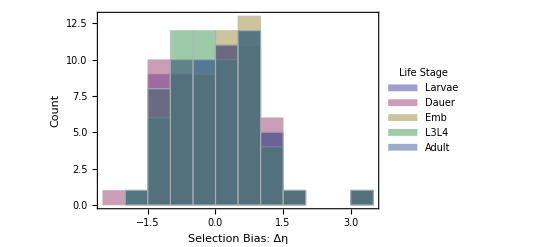

delta.eta.histograms.svg

{{0,0.939803},{0,0.972347},{0,0.926577},{0,0.870732},{0,0.927412}}

```mathematica
scaledDataLabeled = Map[Flatten[#]&, Table[deltaEtaByAA[aa], {aa, aaVals}] //Transpose ]//Transpose;

transposedScaledData = Drop[Transpose[scaledDataLabeled], 1] ;
(*put data in original format of lifestage = column *)
scaledData = Transpose[transposedScaledData];
hist = Histogram[transposedScaledData, 
ChartStyle->ColorData[1],
ChartLegends->SwatchLegend[
stages, 
LegendLabel->"Life Stage",
LegendFunction->"Frame"
],
Background->White,
FrameLabel->{"Selection Bias: Δη", "Count"}
]

Export["delta.eta.histograms.svg", hist, Background->White]

Map[{Chop[Mean[#]], StandardDeviation[#]}&, transposedScaledData]
```

```mathematica
?Pastel
```

Information::notfound: Symbol Pastel not found.

```mathematica
Map[ColorData, ColorData[] ]
```

{{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113},{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe},{BlackBodySpectrum,HypsometricTints,VisibleSpectrum}}

```mathematica
Options[Histogram]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→GrayLevel[0.85],ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→{True,True,False,False},FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→Automatic,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
?Legend
```

Information::notfound: Symbol Legend not found.

```mathematica
?Chop
```

Chop[expr] replaces approximate real numbers in expr that are close to zero by the exact integer 0.

```mathematica
Transpose[scaledData]
```

{{1.18332,-1.40284,0.302239,-0.082723,-0.767962,0.767962,-0.456264,0.456264,1.0033,-1.0033,-0.637945,0.637945,-0.890498,-0.373005,1.04654,0.216965,-0.797159,0.797159,0.974894,-0.941547,-0.0333463,1.12365,-1.12365,0.319015,-1.95293,-1.22894,-0.36036,3.34777,-0.12456,-0.694159,0.694159,0.740284,-1.22233,-0.0295892,0.51163,0.639384,-0.639384,0.016241,0.671661,0.0536616,-1.32506,0.955099,-0.371601,1.26119,-1.05492,-0.47523,0.268961,0.950046,-1.3157,0.337922,0.0277292,1.69582,-1.10849,-0.597016,0.00968877,-0.700961,0.700961,-0.393632,0.393632},{1.2386,-1.44388,0.26151,-0.0562313,-0.754337,0.754337,-0.461114,0.461114,1.01409,-1.01409,-0.691162,0.691162,-0.94236,-0.427716,1.17987,0.190208,-0.815922,0.815922,1.0925,-1.0227,-0.0698021,1.12958,-1.12958,0.39898,-2.05189,-1.26067,-0.404359,3.45888,-0.140936,-0.69028,0.69028,0.753721,-1.23562,-0.0783826,0.560278,0.654211,-0.654211,0.0993808,0.820435,0.006073,-1.40341,0.920998,-0.443478,1.25943,-1.04409,-0.535721,0.320381,0.944273,-1.3016,0.273885,0.0834397,1.75578,-1.15101,-0.606759,0.00199556,-0.735699,0.735699,-0.402773,0.402773},{1.15805,-1.43667,0.363004,-0.0843848,-0.743382,0.743382,-0.45918,0.45918,0.985239,-0.985239,-0.653749,0.653749,-0.907635,-0.330282,1.07151,0.166403,-0.782077,0.782077,0.991363,-0.942231,-0.0491317,1.12835,-1.12835,0.306986,-1.9349,-1.16437,-0.384735,3.30938,-0.132361,-0.701248,0.701248,0.672386,-1.20166,0.0129776,0.516301,0.624732,-0.624732,0.0220083,0.691116,0.0502972,-1.26259,0.902138,-0.402971,1.1998,-1.04736,-0.424396,0.271961,0.910291,-1.31974,0.373424,0.0360269,1.6348,-1.0798,-0.561855,0.00685149,-0.697738,0.697738,-0.359283,0.359283},{1.0928,-1.31348,0.282567,-0.0618866,-0.680911,0.680911,-0.416421,0.416421,0.933458,-0.933458,-0.600841,0.600841,-0.862596,-0.324133,1.0276,0.159128,-0.742547,0.742547,0.932334,-0.85694,-0.0753943,1.05259,-1.05259,0.30131,-1.82611,-1.12075,-0.371108,3.12932,-0.112655,-0.628758,0.628758,0.737855,-1.18251,-0.00787737,0.452536,0.604577,-0.604577,0.0403875,0.63773,-0.045406,-1.16708,0.865414,-0.331042,1.124,-0.97126,-0.413212,0.26047,0.854086,-1.19716,0.284901,0.0581698,1.55841,-0.982615,-0.571394,-0.00440201,-0.646685,0.646685,-0.315707,0.315707},{1.18467,-1.43285,0.301107,-0.052927,-0.733615,0.733615,-0.465748,0.465748,0.992923,-0.992923,-0.668995,0.668995,-0.904509,-0.333546,1.05586,0.182193,-0.790171,0.790171,1.04339,-0.990863,-0.0525239,1.14066,-1.14066,0.332665,-1.92506,-1.15845,-0.401183,3.25887,-0.106851,-0.70096,0.70096,0.685831,-1.20818,-0.00796786,0.530318,0.630509,-0.630509,0.0909135,0.643511,0.0413944,-1.27584,0.872798,-0.372772,1.21495,-1.06577,-0.441003,0.291822,0.934599,-1.32979,0.344622,0.0505701,1.62606,-1.06694,-0.574637,0.015515,-0.717515,0.717515,-0.365105,0.365105}}

```mathematica
Options[Histogram]
?Histogram
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→GrayLevel[0.85],ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→{True,True,False,False},FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→Automatic,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

```mathematica
?Normalize
```

Normalize[v] gives the normalized form of a vector v. 
Normalize[z] gives the normalized form of a complex number z.
Normalize[expr,f] normalizes with respect to the norm function f.

```mathematica
aaPos
```

{{58},{59}}

```mathematica
?Position
```

Position[expr,pattern] gives a list of the positions at which objects matching pattern appear in expr. 
Position[expr,pattern,levelspec] finds only objects that appear on levels specified by levelspec. 
Position[expr,pattern,levelspec,n] gives the positions of the first n objects found. 
Position[pattern] represents an operator form of Position that can be applied to an expression.